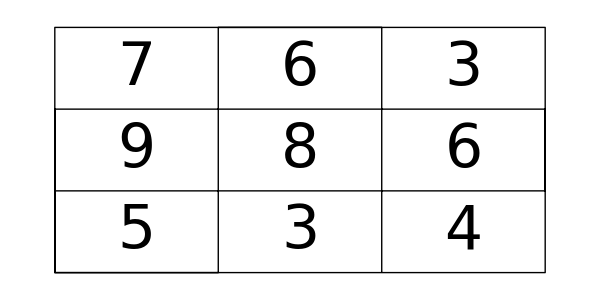

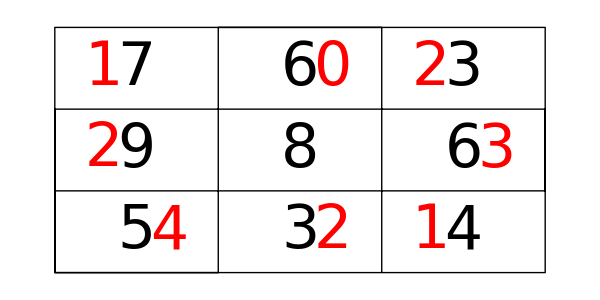

```mathematica
pic[L_]:=Style[Graphics[{
Table[Text[StyleForm[L[[i,j]],FontSize->20],{2i-1,j-1/2}],{i,1,3},{j,1,3}],
Line[{{0,0},{0,3},{6,3},{6,0},{0,0},{0,1},{6,1},{6,2},{0,2},{0,0},{2,0},{2,3},{4,3},{4,0}}]
},ImageSize->200],Antialiasing->False]
```

```mathematica
answer[s_,rows_]:=Style[Graphics[{
Table[Text[StyleForm[s[[i,j]],FontSize->20],{2i-1,j-1/2}],{i,1,3},{j,1,3}],
Line[{{0,0},{0,3},{6,3},{6,0},{0,0},{0,1},{6,1},{6,2},{0,2},{0,0},{2,0},{2,3},{4,3},{4,0}}],
Red,Table[If[s[[i,j]]==rows[[i,j]],{},If[s[[i,j]]==Mod[rows[[i,j]],10],Text[StyleForm[Floor[rows[[i,j]]/10],FontSize->20],{2i-1.4,j-1/2}],Text[StyleForm[Mod[rows[[i,j]],10],FontSize->20],{2i-.6,j-1/2}]]],{i,1,3},{j,1,3}]
},ImageSize->200],Antialiasing->False]
```

```mathematica
strip[n_]:=Module[{t},
t=IntegerDigits[n];
If[Mod[n,10]==0,n/10,
t[[RandomInteger[{1,Length[t]}]]]]]
```

```mathematica
poss[n_]:=Union[Table[10i+n,{i,0,9}]~Join~Table[10n+i,{i,0,9}]]
```

```mathematica
unique[L_]:=Module[{m1,s1,m2,s2,m3,s3,out,out2},
m1=Map[poss,L[[1]],2];
s1=Select[Flatten[Outer[List,Apply[Sequence,m1]],2],Total[#]==100&];
m2=Map[poss,L[[2]],2];
s2=Select[Flatten[Outer[List,Apply[Sequence,m2]],2],Total[#]==100&];
m3=Map[poss,L[[3]],2];
s3=Select[Flatten[Outer[List,Apply[Sequence,m3]],2],Total[#]==100&];
out=Flatten[Outer[List,s1,s2,s3,1],2];
out2=Select[out,Total[#]=={100,100,100}&]
]
```

```mathematica
For[i=1,i>0,i++,
c=2;
While[c=!=1||Length[Select[Flatten[rows],#<10&]]>2,
rows=Table[0,{3},{3}];
While[(*9<Min[Flatten[rows]]||*)Min[Flatten[rows]]≤0||Length[Union[Flatten[rows]]]<9||Total[rows[[1]]]=!=100,
r1=RandomInteger[{1,97}];
r2=RandomInteger[{1,98-r1}];
row1={r1,r2,100-r1-r2};
r3=RandomInteger[{1,97}];
r4=RandomInteger[{1,98-r3}];
row2={r3,r4,100-r3-r4};
row3=100-row1-row2;
rows=Transpose[{row1,row2,row3}]];
If[Random[]<1/3,rows={rows[[3]],rows[[2]],rows[[1]]}];
If[Random[]<1/3,rows={rows[[1]],rows[[3]],rows[[2]]}];
s=Map[strip,rows,{2}];
u=unique[s];
c=Length[u]];
Print[pic[s]];Print[answer[s,rows]]]
```

```mathematica
For[i=1,i>0,i++,(* all two digits *)
c=2;
While[c=!=1||Length[Select[Flatten[rows],#<10&]]>2,
rows=Table[0,{3},{3}];
While[10>Min[Flatten[rows]]||Min[Flatten[rows]]≤0||Length[Union[Flatten[rows]]]<9||Total[rows[[1]]]=!=100,
r1=RandomInteger[{1,97}];
r2=RandomInteger[{1,98-r1}];
row1={r1,r2,100-r1-r2};
r3=RandomInteger[{1,97}];
r4=RandomInteger[{1,98-r3}];
row2={r3,r4,100-r3-r4};
row3=100-row1-row2;
rows=Transpose[{row1,row2,row3}]];
If[Random[]<1/3,rows={rows[[3]],rows[[2]],rows[[1]]}];
If[Random[]<1/3,rows={rows[[1]],rows[[3]],rows[[2]]}];
s=Map[strip,rows,{2}];
u=unique[s];
c=Length[u]];
Print[pic[s]];Print[answer[s,rows]]]
```

## no single digits

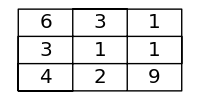

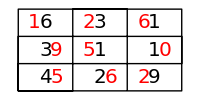

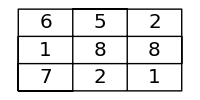

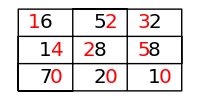

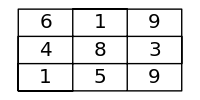

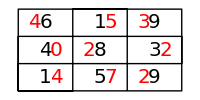

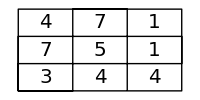

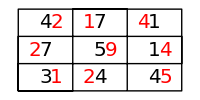

## one single digit